## Constants

```mathematica
Get["constants.m"]
```

```mathematica
SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb/"];
```

## Get QM

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/siteone";
```

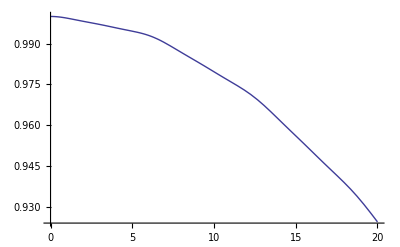

```mathematica
QMS1=%;
```

## Get Wig SU3

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj10010t";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj100ht";
```

```mathematica
Get[su3outfile];
```

```mathematica
Dimensions[avgspins]
```

{128,3,8}

```mathematica
avgspins3=avgspins;
```

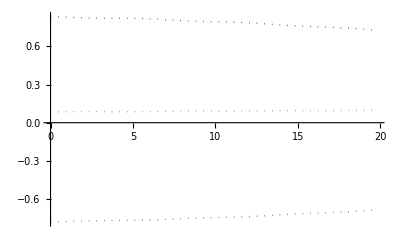

```mathematica
TWAsu3=ListPlot[Table[{times,2avgspins3[[All,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted]
```

## Get Wig SU2

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/su2dw6ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/sofarsu2";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su2dw6uj1001m";
```

```mathematica
avgspins2=%;
```

```mathematica
Dimensions[avgspins2]
```

{128,6,3}

```mathematica
TWAsu2=ListPlot[{{times,avgspins2[[All,1,3]]}ᵀ,{times,avgspins2[[All,4,3]]}ᵀ},Joined->True,PlotStyle->Dashed];
```

## Plots

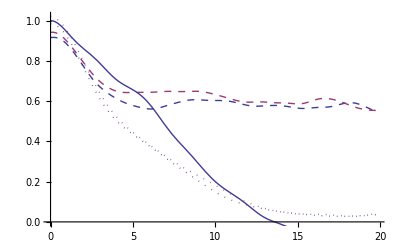

```mathematica
Show[TWA6,TWAsu2,szplus6]
```

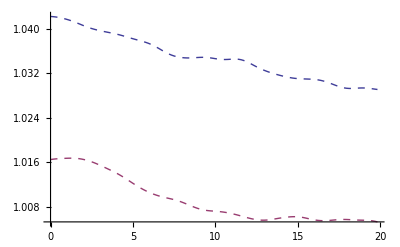

```mathematica
Show[TWAsu2]
```

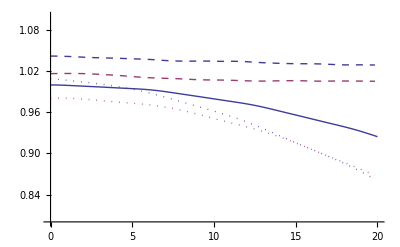

```mathematica
Show[TWAsu2,TWAsu3,QMS1,PlotRange->{0.8,1.1},AxesOrigin->{0,0.8}]
```